## Invoice

Getting the data from the invoice.csv file (may take a few seconds)

We import the Data from the invoice.csv file,

Take the headers from the first row of the csv file

build a list of associations(Key-Value datastructures) to be fed into a Dataset

Create a Dataset (like dataframe from pandas) invoice

```mathematica
csv=Import[FileNameJoin[{NotebookDirectory[],"data_code","invoice.csv"}]];
headers=First[csv];
assoc=Association[Thread[headers->#]]&/@Rest[csv];
invoice=Dataset[assoc];
Clear[assoc]
```

Getting the data from the items.csv

We import the Data from the item.csv file,

Take the headers from the first row of the csv file and call it headersItem

build a list of associations(Key-Value datastructures) to be fed into a Dataset

Create a Dataset (like dataframe from pandas) item

```mathematica
csvItem=Import[FileNameJoin[{NotebookDirectory[],"data_code","item.csv"}]];
headersItem=First[csvItem];
assocItem=Association[Thread[headersItem->#]]&/@Rest[csvItem];
item=Dataset[assocItem];
Remove[assocItem]
```

Getting the data from the review.csv (put together using datMerger.nb)

We import the Data from the review.csv file,

Take the headers from the first row of the csv file and call it headersItem

build a list of associations(Key-Value datastructures) to be fed into a Dataset

Create a Dataset (like dataframe from pandas) item

```mathematica
csvReview=Import[FileNameJoin[{NotebookDirectory[],"reviews","review.csv"}]];
headersReview=First[csvReview];
assocReview=Association[Thread[headersReview->#]]&/@Rest[csvReview];
review=Dataset[assocReview];
Remove[assocReview]
```

Here we look at the lengths of the datasets

```mathematica
{Length[invoice],Length[item],Length[review]}
```

{930508,4166,50000}

and the names of the headers for each

```mathematica
headers
```

{Invoice_id,Date,Item_id,Vendor_id,Vendor_Name,Store_id,Store_Name,Address,City_Name,Zip_Code,County_id,County_Name,Bottles_Sold}

```mathematica
headersItem
```

{Item_id,Item_Description,Category,Pack,Bottle_Volume_ml,Bottle_Cost,Bottle_Retail_Price}

```mathematica
headersReview
```

{Customer_id,Invoice_id,Product_Rating}

we see that invoice and item share the “Item_Id” tag so we would like to merge them into one, Using JoinAccross.  This takes a few seconds.

```mathematica
itemInvoice=JoinAcross[invoice,item,"Item_id"];
```

The following is an example on how to add a new column keyed under “Purchase_Cost” obtained from the product of the “Bottles_Sold” value with the “Bottle_Retail_Price”.

```mathematica
RandomChoice[itemInvoice]/.x_Association:>Association[x,"Purchase_Cost"->x["Bottle_Retail_Price"] x["Bottles_Sold"]]
```

We can do the above to the whole mixed Dataset (takes a few seconds)

```mathematica
withPurchaseCost=(itemInvoice/.x_Association:>Association[x,"Purchase_Cost"->x["Bottle_Retail_Price"] x["Bottles_Sold"]]);
```

We can see with an example what the result looks like. Pay special attention to the Purchase_Cost

```mathematica
RandomChoice[withPurchaseCost]
```

The length of the latest Dataset should be the same as the one from the original invoices

```mathematica
Length[withPurchaseCost]==Length[invoice]
```

True

### Invoice

We can look at the cities surveyed

```mathematica
invoice[Counts,"City_Name"]
```

Since they are only two an interesting analysis would be to separate them and look at their respective statistics maybe we will come back to that later

We can take out a count by date (# of purchases per day)

```mathematica
invoice[Counts,"Date"]
```

And get a time series plot

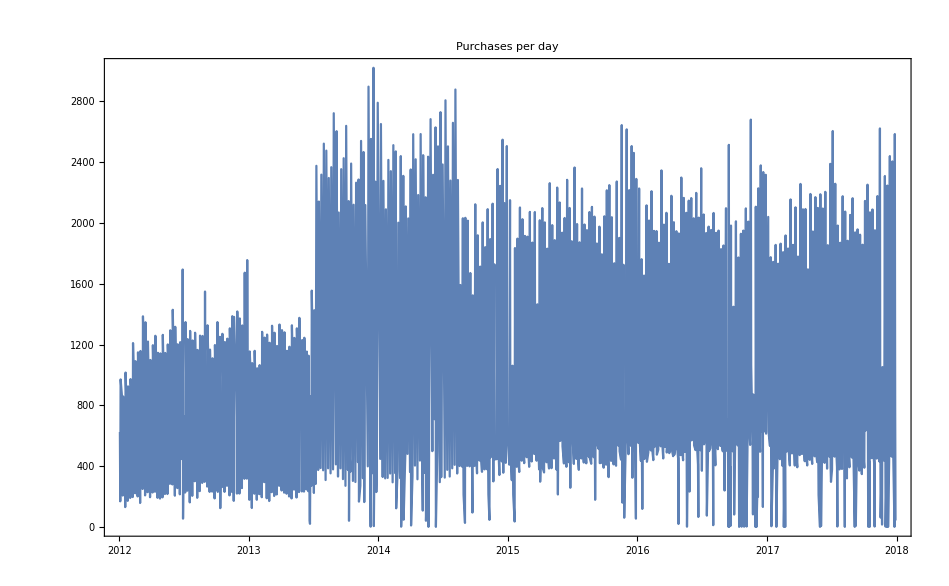

```mathematica
DateListPlot[invoice[Counts,"Date"],PlotLabel->"Purchases per day"]
```

The above is interesting, as it shows that something occurred around mid-2013 that shot sales per day up.

We can look at a moving average to see more general trends.

```mathematica
MovingAverage[Values[invoice[Counts,"Date"]]//Normal,5]
```

1017

```mathematica
(Keys[invoice[Counts,"Date"]]//Normal)[[5;;]]//Length
```

1017

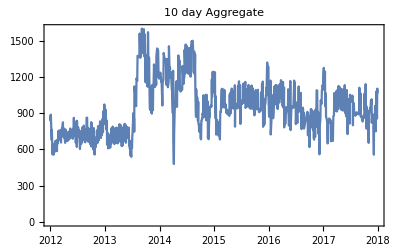

```mathematica
DateListPlot[Association[Thread[(Keys[invoice[Counts,"Date"]]//Normal)[[10;;]]->MovingAverage[Values[invoice[Counts,"Date"]]//Normal,10]]],PlotLabel->"10 day Aggregate"]
```

Let us check the type of objects we have

```mathematica
Head/@invoice[[1]]
```

```mathematica
Keys[Head/@invoice[[1]]]//Normal
```

{Invoice_id,Date,Item_id,Vendor_id,Vendor_Name,Store_id,Store_Name,Address,City_Name,Zip_Code,County_id,County_Name,Bottles_Sold}

```mathematica
invoice[Counts,#]&/@{"Date","Item_id","Vendor_id","Vendor_Name","Store_id","Store_Name","Address","City_Name","Zip_Code","County_id","County_Name","Bottles_Sold"}
```

{,,,,,,,,,,,}

There seems to be one unsold item

```mathematica
{(invoice[Counts, "Item_id"]//Length) ,(item//Length)}
```

{4165,4166}

```mathematica
Complement[Normal[item[All,"Item_id"]],invoice[All, "Item_id"]//Normal//Union]
```

{103}

```mathematica
Select[item,#["Item_id"]==103&]
```

In terms of pure numerical interesting raw data that would be the Bottles Sold, as the rest is mostly identifiers we will work on information about specific identifiers later

```mathematica
invoice[Counts,"Bottles_Sold",Head]
```

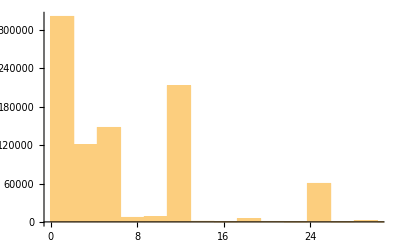

```mathematica
invoice[Histogram,"Bottles_Sold"]
```

If wanted we can adjust the bin counts

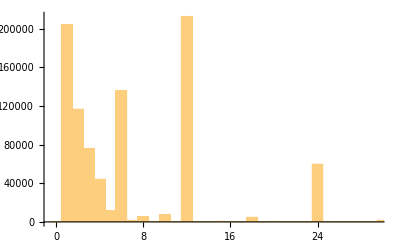

```mathematica
Histogram[invoice[All,"Bottles_Sold"],PlotRange->All]
```

```mathematica
Manipulate[Histogram[invoice[Select[#,#>n&]&,"Bottles_Sold"]],{n,0,1200,100}]
```

The good thing is that it is all integer data, so we can calculate Mean, Standard deviation, min and max

```mathematica
invoice[#,"Bottles_Sold",N]&/@{Mean,StandardDeviation,Min,Max}
```

{9.87565,22.4892,0.,2160.}

0 bottles sold is strange, so let us check those specific invoices

```mathematica
Select[invoice,#["Bottles_Sold"]==0&]//Length
```

73

```mathematica
Select[invoice,#["Bottles_Sold"]==0&]
```

```mathematica
Select[invoice,#["Bottles_Sold"]==2160&]
```

```mathematica
Select[withPurchaseCost,#["Bottles_Sold"]==2160&]
```

We can quickly see which ones were the ones with the lowest number of sales and the largest

```mathematica
Sort[invoice[Counts,"Store_Name"]]
```

Let us check the sales at the Artisan Craft Soda store

```mathematica
Select[invoice,#["Store_Name"]=="Artisan Craft Soda"&]
```

```mathematica
Select[itemInvoice,#["Store_Name"]=="Artisan Craft Soda"&]
```

Let us go back to the invoice data

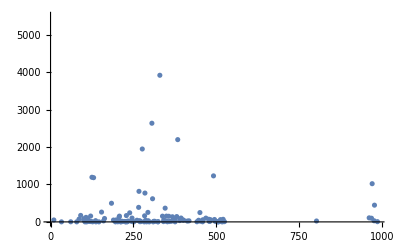

```mathematica
ListPlot[invoice[Counts,"Vendor_id"]]
```

It seems like most of the vendors are under the 4000 count in sales

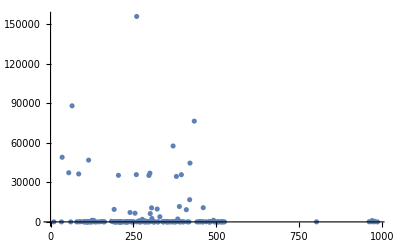

```mathematica
ListPlot[invoice[Counts,"Vendor_id"],PlotRange->All]
```

Although a few of them are way past that number

```mathematica
Max[invoice[Counts,"Vendor_id"]]
```

156106

```mathematica
Select[invoice[Counts,"Vendor_id"]//Normal,#==156106&]
```

<|260→156106|>

```mathematica
invoice[Select[#,#["Vendor_id"]==260&]&]
```

Dataset[<>]

Inuyasha brands having the biggest number of sales

```mathematica
item[[2000,1]]
```

43034

### Item

Let’s look at the data we could work with

```mathematica
Head/@item[[1]]
```

we can look at the different possible pack numbers

```mathematica
KeySort[item[Counts,"Pack"]]
```

Different Categories

```mathematica
Sort[item[Counts,"Category"]]
```

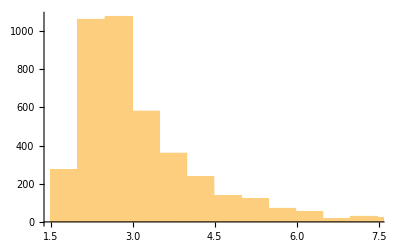

```mathematica
item[Histogram,"Bottle_Cost"]
```

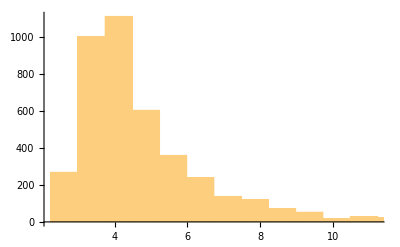

```mathematica
item[Histogram,"Bottle_Retail_Price"]
```

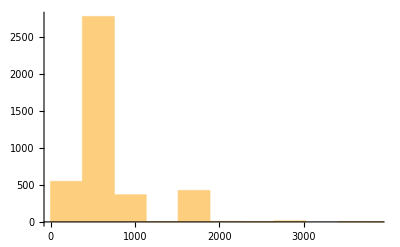

```mathematica
item[Histogram,"Bottle_Volume_ml"]
```

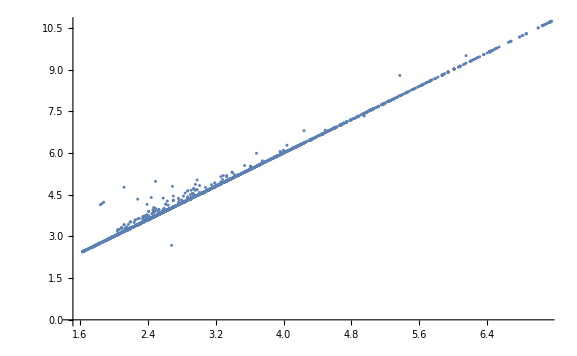

```mathematica
item[ListPlot,{"Bottle_Cost","Bottle_Retail_Price"}]
```

```mathematica
item[Max,"Bottle_Volume_ml"]
```

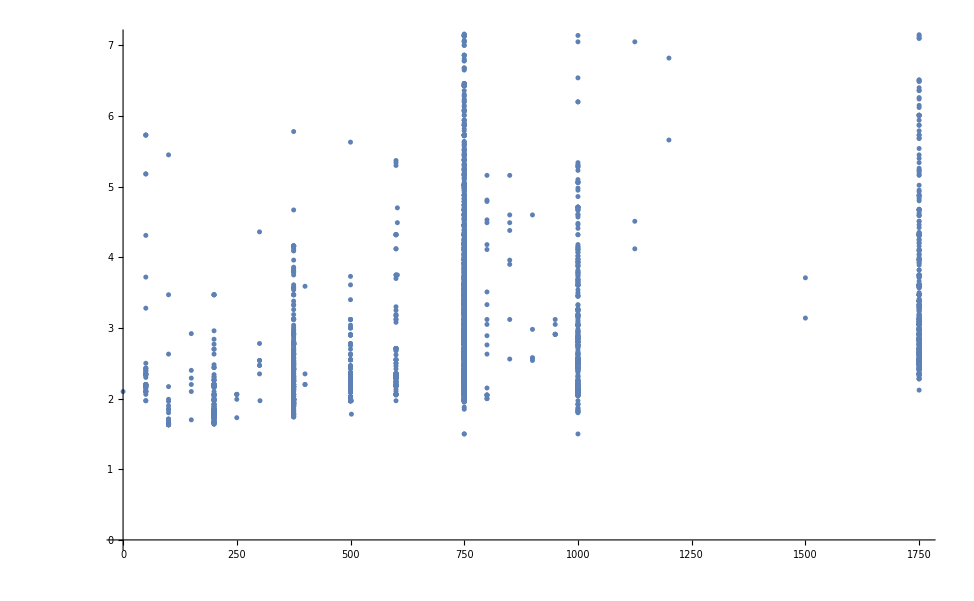

```mathematica
item[ListPlot,{"Bottle_Volume_ml","Bottle_Cost"}]
```

We can plot the whole spectrum

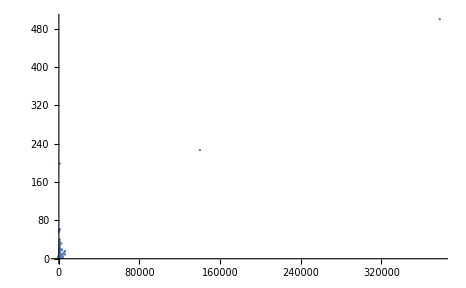

```mathematica
ListPlot[item[All,{"Bottle_Volume_ml","Bottle_Cost"}],PlotRange->All]
```

But we really loose interesting information

```mathematica
data=item[All,{"Bottle_Cost","Bottle_Retail_Price"}]//Normal//Values;
```

```mathematica
LinearModelFit[item[All,{"Bottle_Cost","Bottle_Retail_Price"}]//Normal//Values,{1,x},x]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{4.32,6.48},{3.33,5.},{10.3,20.1},{4.44,6.66},{3.12,4.68},{3.92,5.88},{3.62,5.43},{2.77,4.16},{2.77,4.16},{2.77,4.16},{2.84,4.26},{3.48,5.22},{2.91,4.36},{4.32,6.48},{2.98,4.47},{2.54,3.81},{3.69,5.54},{3.96,5.94},4130,{2.16,3.24},{9.48,14.22},{3.94,5.91},{500.,750.},{2.35,3.53},{3.58,5.37},{3.86,5.79},{8.55,12.82},{9.,13.5},{40.25,60.38},{3.54,5.31},{19.99,29.99},{6.08,9.12},{12.6,18.9},{4.27,6.41},{5.87,8.81},{3.72,5.58},{6.81,10.22}},{1,x},x]
 |  |  |  |

```mathematica
Counts[Map[Head,data,{2}]]
```

<|{Real,Real}→4163,{Real,String}→3|>

```mathematica
DeleteCases[data,{_Real,_String}]
```

```mathematica
Counts[Map[Head,DeleteCases[data,{_Real,_String}],{2}]]
```

<|{Real,Real}→4163|>

```mathematica
model=LinearModelFit[DeleteCases[data,{_Real,_String}],{1,x},x]
```

FittedModel[0.0104165+1.49998 x]

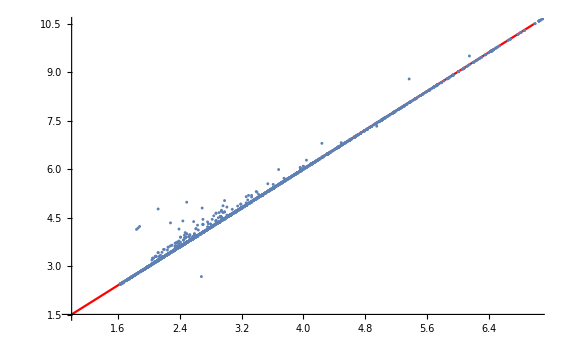

```mathematica
Show[Plot[model[x],{x,1,7},PlotStyle->Red],item[ListPlot,{"Bottle_Cost","Bottle_Retail_Price"}]]
```

```mathematica
Position[data,{_Real,_String}]
```

{{2176},{2355},{2475}}

```mathematica
item[[{2176,2355,2475}]]
```

```mathematica
Position[item[All,"Category"],""]
```

{{3},{3603},{3604},{3605}}

```mathematica
#["Item_Description"]&/@item[[{3,3603,3604,3605}]]
```

```mathematica
Normal@%
```

{Yummy Surstromming Juice,Miku's Leek Juice,Dark Fantasy,Butterbeer}

```mathematica
item[Counts,"Category"]
```

```mathematica
Length[item]
```

4166

```mathematica
item[[19]]
```

```mathematica
item[Union,"Item_Description"]//Length
```

4166

```mathematica
Length[item]
```

4166

## Observations

The cost price relationship is roughly linear as  price ~ 0.0104165+1.49998 Cost

There are 12 different categories of drink and some are not labeled into a category (Yummy Surstromming Juice, Miku’s Leek Juice, Dark Fantasy, Butterbeer)